```mathematica
fsemi[x_]:=√(1-x^2)
fabs[x_]:=Abs[x]
fsin[x_]:=Sin[x]
```

```mathematica
LeftNostrilTop[x_]:=fsemi[x-2]
RightNostrilTop[x_]:=LeftNostrilTop[-x]
LeftNostrilBottom[x_]:=-fsemi[x-2]
RightNostrilBottom[x_]:=LeftNostrilBottom[-x]
NoseTop[x_]:=fsemi[x/5]*2
NoseBottom[x_]:=-NoseTop[x]
LeftEyeTop[x_]:=fsemi[x+4]+4
LeftEyeBottom[x_]:=-fsemi[x+4]+4
RightEyeTop[x_]:=fsemi[x-4]+4
RightEyeBottom[x_]:=-fsemi[x-4]+4
HeadTop[x_]:=fsemi[x/7]*7+2
HeadBottom[x_]:=-fsemi[x/7]*7+2
EarRight[x_]:=-Piecewise[{{fabs[-x/2+1.5],-1≤-x/2+1.5≤0.6},{-100,-x/2+1.5<-1},{-100,-x/2+1.5>0.6}}]*4+11.1
EarLeft[x_]:=-Piecewise[{{fabs[x/2+1.5],-1≤x/2+1.5≤0.6},{-100,x/2+1.5<-1},{-100,x/2+1.5>0.6}}]*4+11.1
BodyTop[x_]:=fsemi[x/10]*10+2.8
BodyBottom[x_]:=-fsemi[x/10]*10+2.8
Tail[x_]:=Piecewise[{{Sin[2x-1]/2,10≤x},{-100,x<10}}]+2
LeftFoot[x_]:=-Piecewise[{{fsemi[-x/2-1.5],-0.87≤-x/2-1.5≤1},{-100,-x/2-1.5<-0.87},{-100,-x/2-1.5>1}}]*3-5.7
RightFoot[x_]:=-Piecewise[{{fsemi[x/2-1.5],-0.87≤x/2-1.5≤1},{-100,x/2-1.5<-0.87},{-100,x/2-1.5>1}}]*3-5.7
```

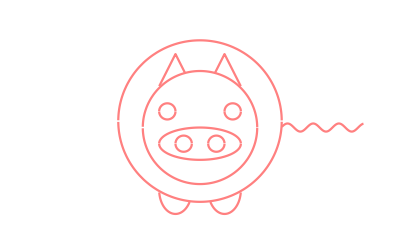

```mathematica
Plot[
{
LeftNostrilTop[x], LeftNostrilBottom[x],
RightNostrilTop[x], RightNostrilBottom[x],
NoseTop[x],NoseBottom[x],
LeftEyeTop[x],LeftEyeBottom[x],
RightEyeTop[x],RightEyeBottom[x],
HeadTop[x], HeadBottom[x],
EarLeft[x], EarRight[x],
BodyTop[x], BodyBottom[x],
Tail[x],
LeftFoot[x],RightFoot[x]
},
{x, -20, 20},
PlotRange->{{-20,20},{-10,15}},
PlotStyle->Pink,
Axes->False
]
```